# Problema 1)

```mathematica
ClearAll["Global`*"]
```

# d)

### Constantes:

```mathematica
g=9.8;
ω=7.292*10^(-5); 
R = 6371*10^3;
H=10;
V0=-5.0;
```

#### Solo la Gravedad:

```mathematica
AzGra=-g;
```

#### Gravedad y Coriolis:

```mathematica
AzGraCor=-g;
AxGraCor[t_,θ_]=-2*ω*Sin[θ]*(V0-g*t);
```

#### Gravedad y Centrífuga:

```mathematica
AzGraCen[z_,θ_]=ω^2*z*Sin[θ]^2-g;
AyGraCen[z_,θ_]=-ω^2*z*Sin[θ]Cos[θ];
```

#### Ambas:

```mathematica
AzGraBoth[z_,θ_]=ω^2*z*Sin[θ]^2-g;
AyGraBoth[z_,θ_]=ω^2*z*Sin[θ]Cos[θ];
AxGraBoth[t_,θ_]=-2*ω*Sin[θ]*(V0-g*t);
```

### Tiempos y Alturas:

```mathematica
Alturas={H/4,H/2,3H/4,H};
Tiempos ={0.133,0.0918,0.0478,0};
```

### Gráficas de Aceleración vs Colatitud:

#### Solo la Gravedad :

#### Eje z:

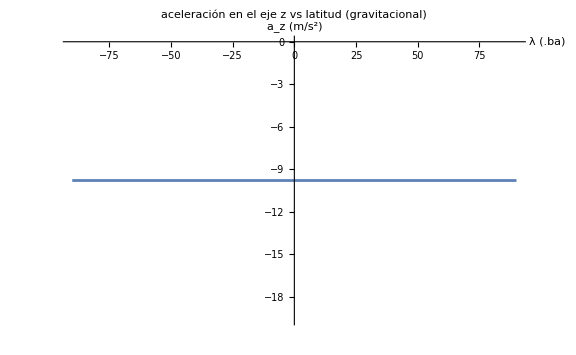

```mathematica
Plot[AzGra,{θ, -90,90}, AxesLabel->{"λ (.ba)", "a_z (m/s^2)"}, ImageSize->Large, PlotLabel->"aceleración en el eje z vs latitud (gravitacional)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Gravedad y Coriolis :

#### Eje z:

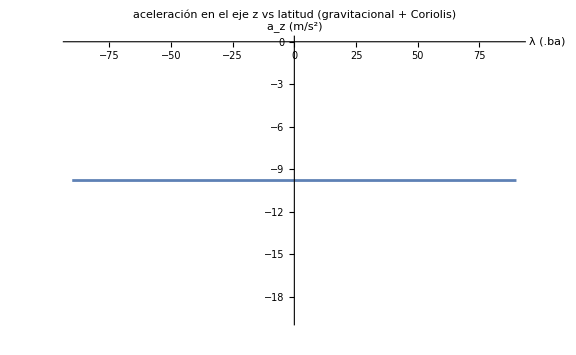

```mathematica
Plot[AzGraCor,{θ, -90,90}, AxesLabel->{"λ (.ba)", "a_z (m/s^2)"}, ImageSize->Large, PlotLabel->"aceleración en el eje z vs latitud (gravitacional + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje x:

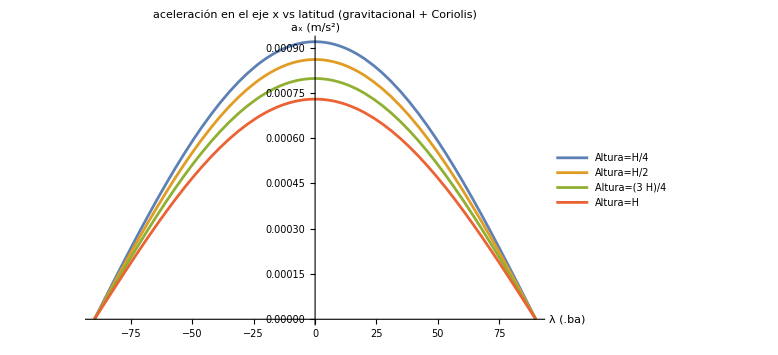

```mathematica
Plots = AxGraCor[#,Degree*(90-θ)]&/@Tiempos;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","a_x (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"aceleración en el eje x vs latitud (gravitacional + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Gravedad y Centrífuga :

#### Eje z:

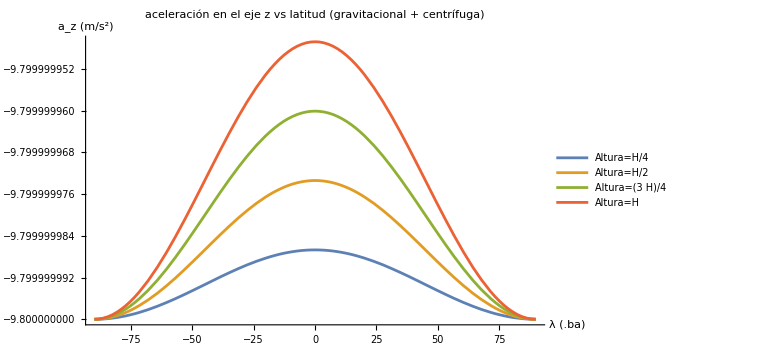

```mathematica
Plots = AzGraCen[#,Degree*(90-θ)]&/@Alturas;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","a_z (m/s^2)"},PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"aceleración en el eje z vs latitud (gravitacional + centrífuga)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje y:

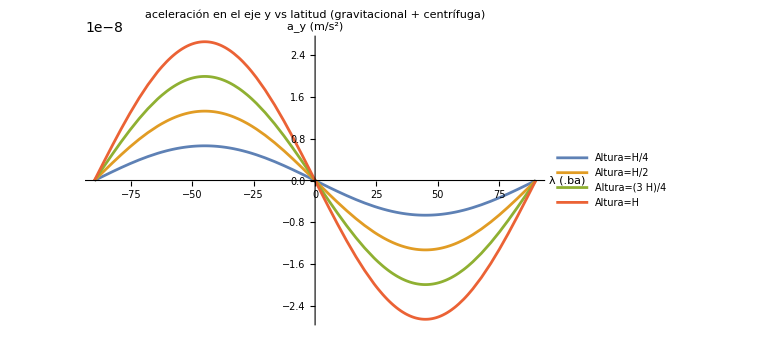

```mathematica
Plots = AyGraCen[#,Degree*(90-θ)]&/@Alturas;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","a_y (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"},ImageSize->Large, PlotLabel->"aceleración en el eje y vs latitud (gravitacional + centrífuga)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Ambas :

#### Eje z:

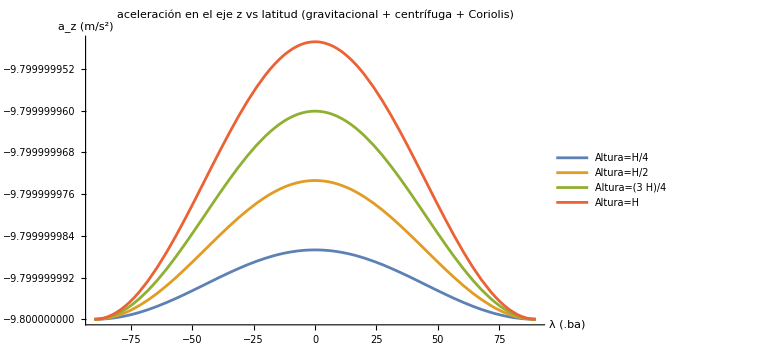

```mathematica
Plots = AzGraBoth[#,Degree*(90-θ)]&/@Alturas;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","a_z (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"},ImageSize->Large, PlotLabel->"aceleración en el eje z vs latitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje y:

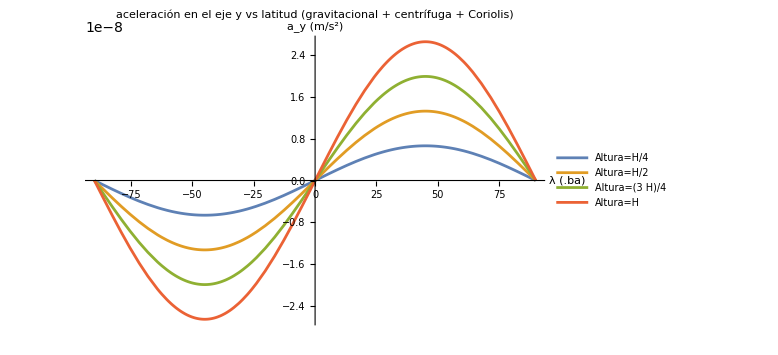

```mathematica
Plots = AyGraBoth[#,Degree*(90-θ)]&/@Alturas;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","a_y (m/s^2)"},PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"aceleración en el eje y vs latitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje x:

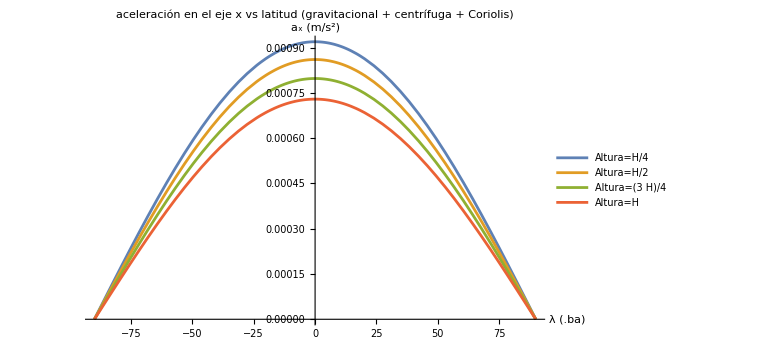

```mathematica
Plots = AxGraCor[#,Degree*(90-θ)]&/@Tiempos;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","a_x (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"aceleración en el eje x vs latitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

### Gráficas de Aceleración vs Longitud:

#### Solo la Gravedad :

#### Eje z :

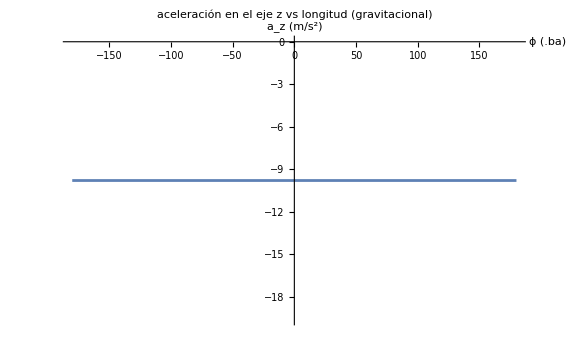

```mathematica
Plot[AzGra,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)", "a_z (m/s^2)"}, ImageSize->Large, PlotLabel->"aceleración en el eje z vs longitud (gravitacional)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Gravedad y Coriolis :

#### Eje z:

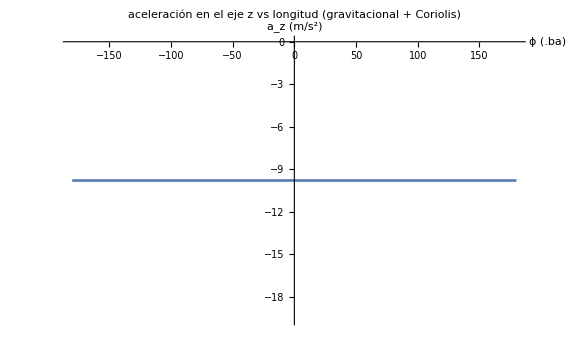

```mathematica
Plot[AzGraCor,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)", "a_z (m/s^2)"}, ImageSize->Large, PlotLabel->"aceleración en el eje z vs longitud (gravitacional + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje x:

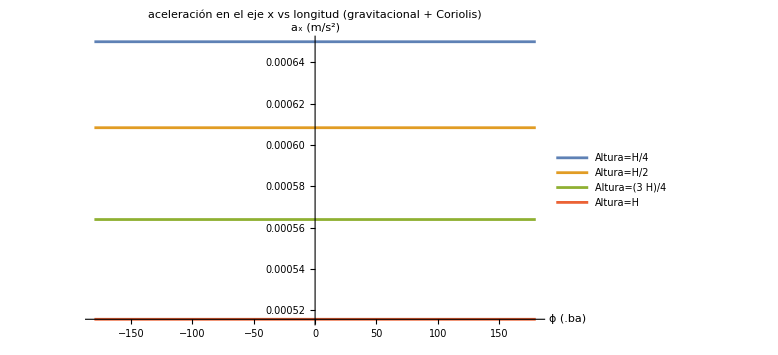

```mathematica
Plots = AxGraCor[#,Degree*45]&/@Tiempos;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","a_x (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"aceleración en el eje x vs longitud (gravitacional + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Gravedad y Centrífuga :

#### Eje z:

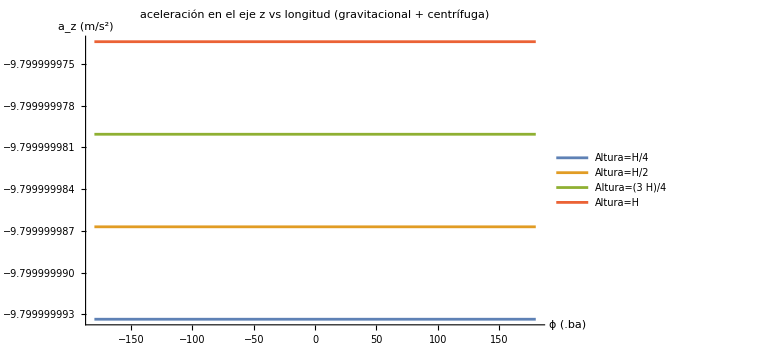

```mathematica
Plots = AzGraCen[#,Degree*45]&/@Alturas;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","a_z (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"},ImageSize->Large, PlotLabel->"aceleración en el eje z vs longitud (gravitacional + centrífuga)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje y:

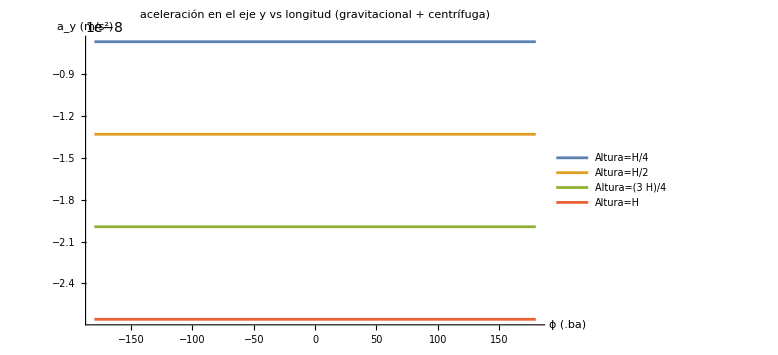

```mathematica
Plots = AyGraCen[#,Degree*45]&/@Alturas;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","a_y (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"},ImageSize->Large, PlotLabel->"aceleración en el eje y vs longitud (gravitacional + centrífuga)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Ambas :

#### Eje z:

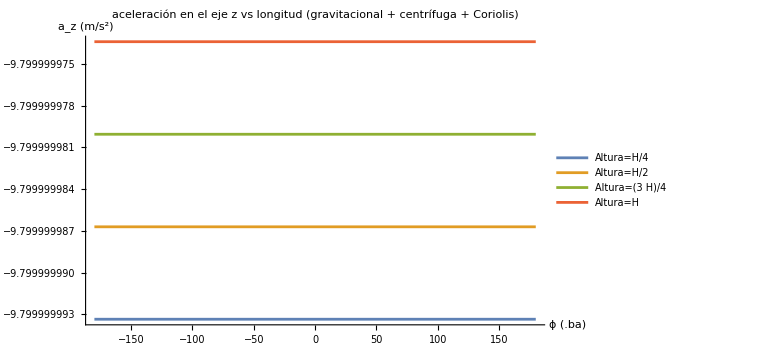

```mathematica
Plots = AzGraBoth[#,Degree*45]&/@Alturas;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","a_z (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"},ImageSize->Large, PlotLabel->"aceleración en el eje z vs longitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje y:

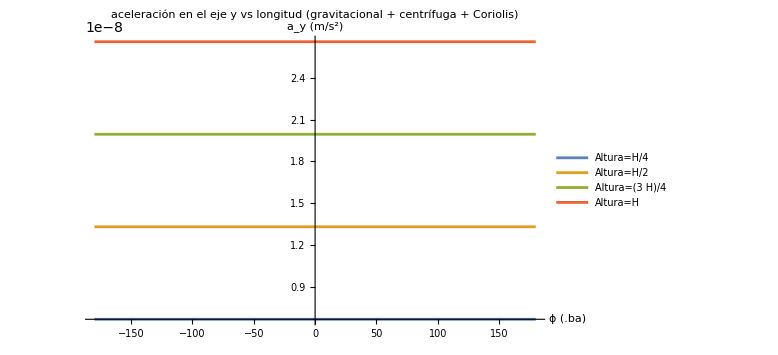

```mathematica
Plots = AyGraBoth[#,Degree*45]&/@Alturas;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","a_y (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"},ImageSize->Large, PlotLabel->"aceleración en el eje y vs longitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje x:

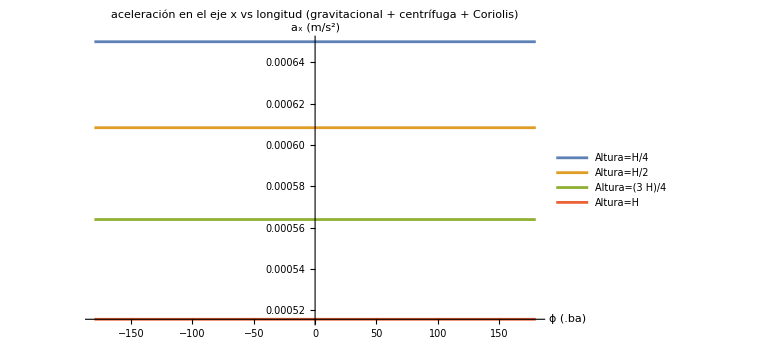

```mathematica
Plots = AxGraBoth[#,Degree*45]&/@Tiempos;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","a_x (m/s^2)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"aceleración en el eje x vs longitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

# d)

#### Solo la Gravedad:

```mathematica
VzGra[t_]=V0-g*t;
```

#### Gravedad y Coriolis:

```mathematica
VzGraCor[t_]=V0-g*t;
VxGraCor[t_,θ_]=-2*ω*Sin[θ]*(V0*t-1/2*g*t^2);
```

#### Gravedad y Centrífuga:

```mathematica
VzGraCen[z_,t_,θ_]=(ω^2*z*Sin[θ]^2-g)*t + V0;
VyGraCen[z_,t_,θ_]=-ω^2*z*Sin[θ]Cos[θ]*t;
```

#### Ambas:

```mathematica
VzGraBoth[z_,t_,θ_]=(ω^2*z*Sin[θ]^2-g)*t + V0;
VyGraBoth[z_,t_,θ_]=-ω^2*z*Sin[θ]Cos[θ]*t;
VxGraBoth[z_,t_,θ_]=-2*ω*Sin[θ]*t(V0+(ω^2*z*Sin[θ]^2-g));
```

### Gráficas de Velocidad vs Colatitud:

#### Solo la Gravedad :

#### Eje z:

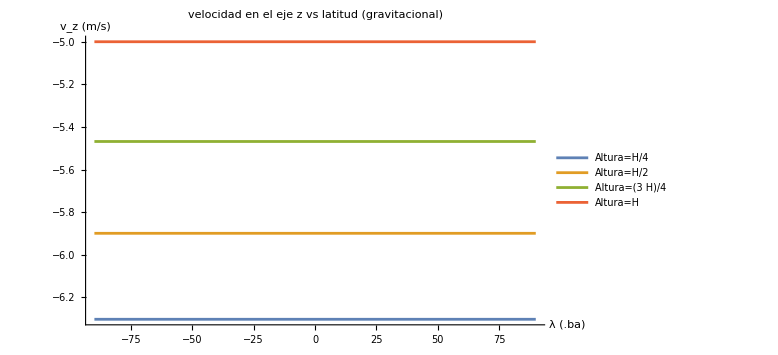

```mathematica
Plots = VzGra[#]&/@Tiempos;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","v_z (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje z vs latitud (gravitacional)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Gravedad y Coriolis :

#### Eje z:

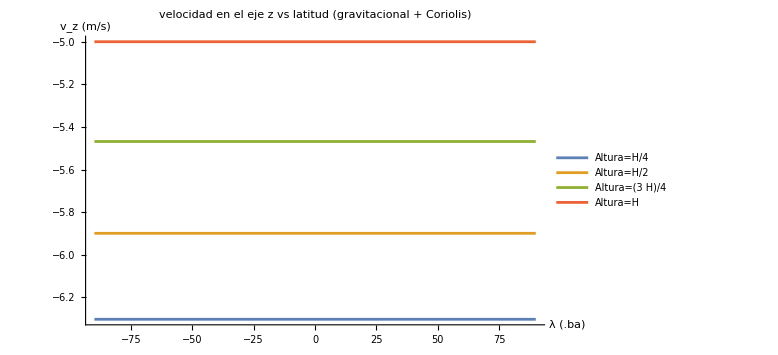

```mathematica
Plots = VzGraCor[#]&/@Tiempos;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","v_z (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje z vs latitud (gravitacional + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje x:

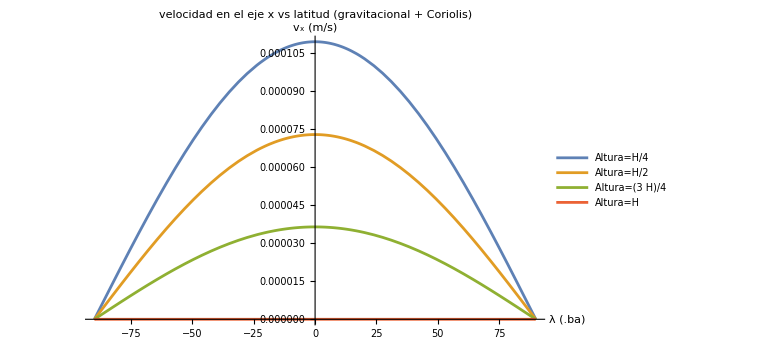

```mathematica
Plots = VxGraCor[#, Degree*(90-θ)]&/@Tiempos;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","v_x (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje x vs latitud (gravitacional + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Gravedad y Centrífuga :

#### Eje z:

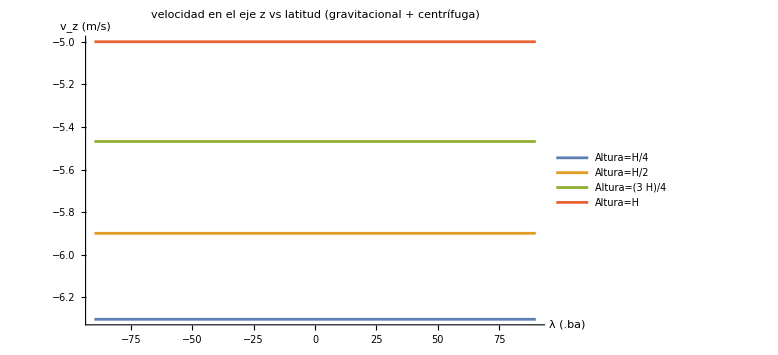

```mathematica
Indice={1,2,3,4};
Plots = VzGraCen[Alturas[[#]],Tiempos[[#]], Degree*(90-θ)]&/@Indice;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","v_z (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje z vs latitud (gravitacional + centrífuga)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje y:

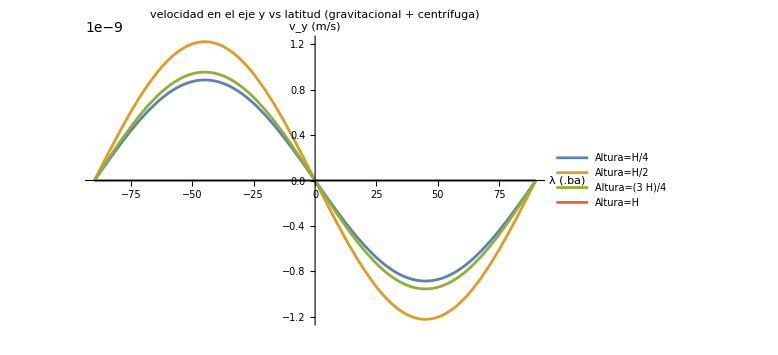

```mathematica
Indice={1,2,3,4};
Plots = VyGraCen[Alturas[[#]],Tiempos[[#]], Degree*(90-θ)]&/@Indice;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","v_y (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje y vs latitud (gravitacional + centrífuga)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Ambas :

#### Eje z:

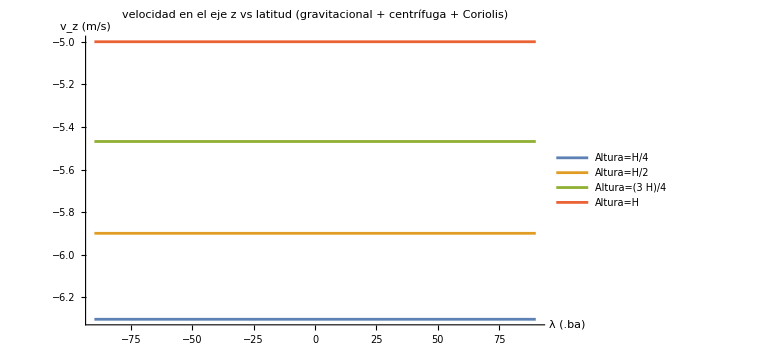

```mathematica
Indice={1,2,3,4};
Plots = VzGraBoth[Alturas[[#]],Tiempos[[#]], Degree*(90-θ)]&/@Indice;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","v_z (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje z vs latitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje y:

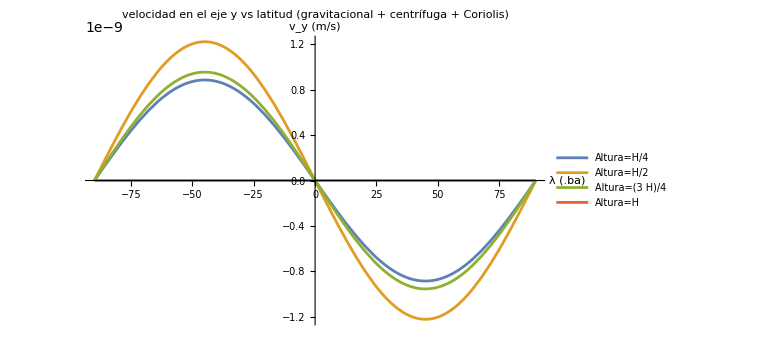

```mathematica
Indice={1,2,3,4};
Plots = VyGraBoth[Alturas[[#]],Tiempos[[#]], Degree*(90-θ)]&/@Indice;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","v_y (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje y vs latitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje x:

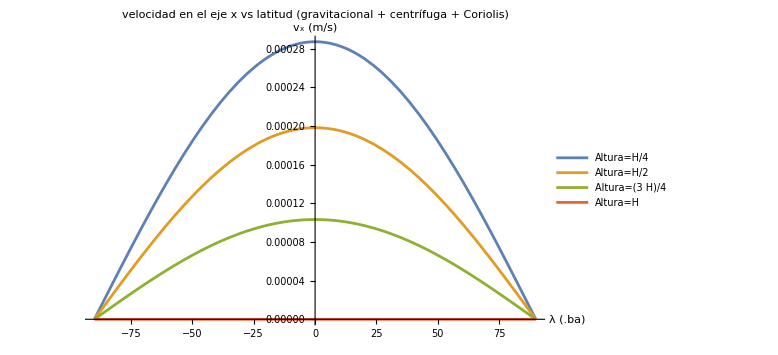

```mathematica
Indice={1,2,3,4};
Plots = VxGraBoth[Alturas[[#]],Tiempos[[#]], Degree*(90-θ)]&/@Indice;
Plot[Plots,{θ, -90,90}, AxesLabel->{"λ (.ba)","v_x (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje x vs latitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

### Gráficas de Velocidad vs Longitud:

#### Solo la Gravedad :

#### Eje z:

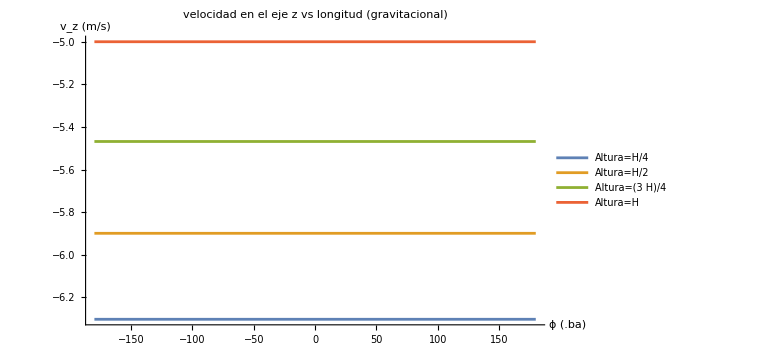

```mathematica
Plots = VzGra[#]&/@Tiempos;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","v_z (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje z vs longitud (gravitacional)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Gravedad y Coriolis :

#### Eje z:

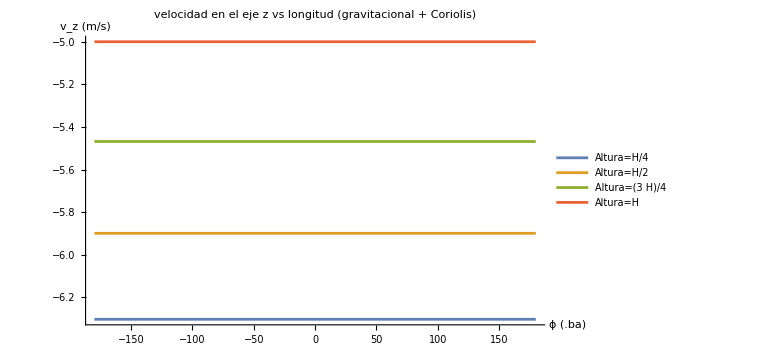

```mathematica
Plots = VzGraCor[#]&/@Tiempos;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","v_z (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje z vs longitud (gravitacional + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje x:

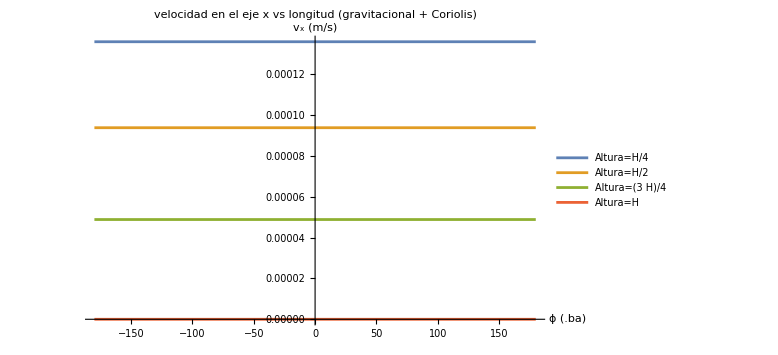

```mathematica
Plots = VxGraCor[#, Degree*45]&/@Tiempos;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","v_x (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje x vs longitud (gravitacional + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Gravedad y Centrífuga :

#### Eje z:

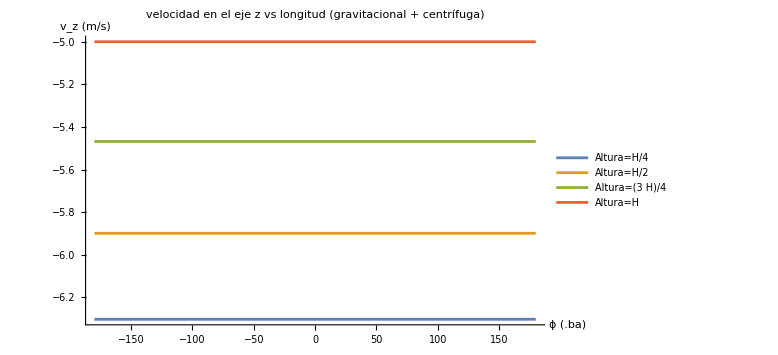

```mathematica
Indice={1,2,3,4};
Plots = VzGraCen[Alturas[[#]],Tiempos[[#]], Degree*(90-45)]&/@Indice;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","v_z (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje z vs longitud (gravitacional + centrífuga)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje y:

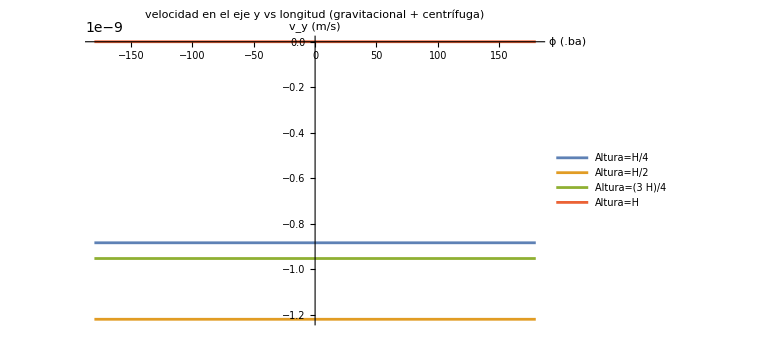

```mathematica
Indice={1,2,3,4};
Plots = VyGraCen[Alturas[[#]],Tiempos[[#]], Degree*(90-45)]&/@Indice;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","v_y (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje y vs longitud (gravitacional + centrífuga)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Ambas :

#### Eje z:

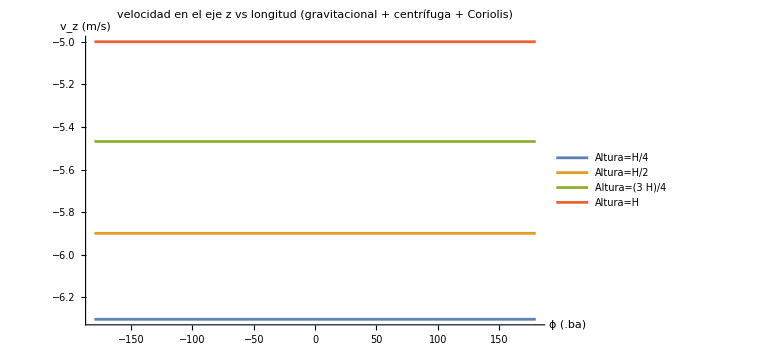

```mathematica
Indice={1,2,3,4};
Plots = VzGraBoth[Alturas[[#]],Tiempos[[#]], Degree*(90-45)]&/@Indice;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","v_z (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje z vs longitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje y:

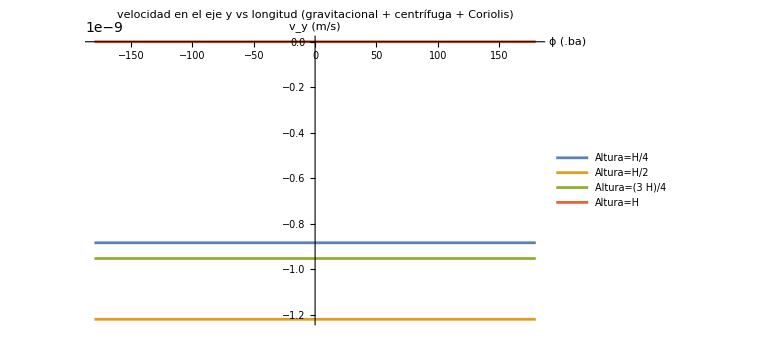

```mathematica
Indice={1,2,3,4};
Plots = VyGraBoth[Alturas[[#]],Tiempos[[#]], Degree*(90-45)]&/@Indice;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","v_y (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje y vs longitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

#### Eje x:

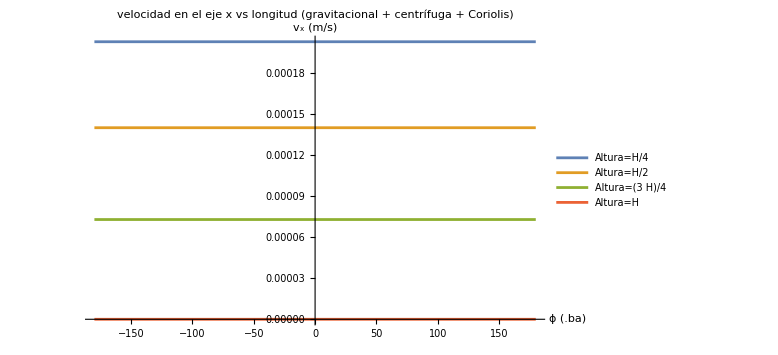

```mathematica
PIndice={1,2,3,4};
Plots = VxGraBoth[Alturas[[#]],Tiempos[[#]], Degree*(90-45)]&/@Indice;
Plot[Plots,{ϕ, -180,180}, AxesLabel->{"ϕ (.ba)","v_x (m/s)"}, PlotLegends->{"Altura=H/4","Altura=H/2","Altura=(3  H)/4","Altura=H"}, ImageSize->Large, PlotLabel->"velocidad en el eje x vs longitud (gravitacional + centrífuga + Coriolis)", BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

```mathematica
outputCells=Cells[CellStyle->"Output"];
cellsWithGraphics=Select[outputCells,!FreeQ[NotebookRead[#],GraphicsBox]&];
MapIndexed[Export[ToString[#2[[1]]]<>".pdf",NotebookRead[#1],"PDF"]&,cellsWithGraphics]
```

{1.pdf,2.pdf,3.pdf,4.pdf,5.pdf,6.pdf,7.pdf,8.pdf,9.pdf,10.pdf,11.pdf,12.pdf,13.pdf,14.pdf,15.pdf,16.pdf,17.pdf,18.pdf,19.pdf,20.pdf,21.pdf,22.pdf,23.pdf,24.pdf,25.pdf,26.pdf,27.pdf,28.pdf,29.pdf,30.pdf,31.pdf,32.pdf}